Eigensystem::maxit2: Warning: the maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

Eigensystem::maxit2: Warning: the maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance or use an estimate as a shift, any of which may help.

General::stop: Further output of Eigensystem::maxit2 will be suppressed during this calculation.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix … in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

General::stop: Further output of Eigensystem::chnpdef will be suppressed during this calculation.

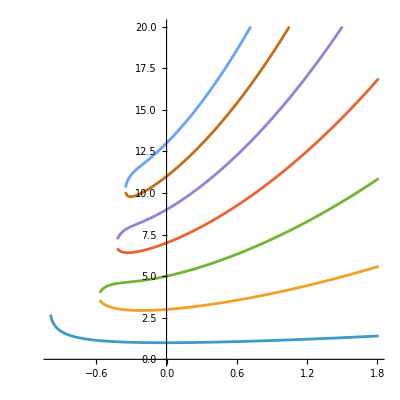

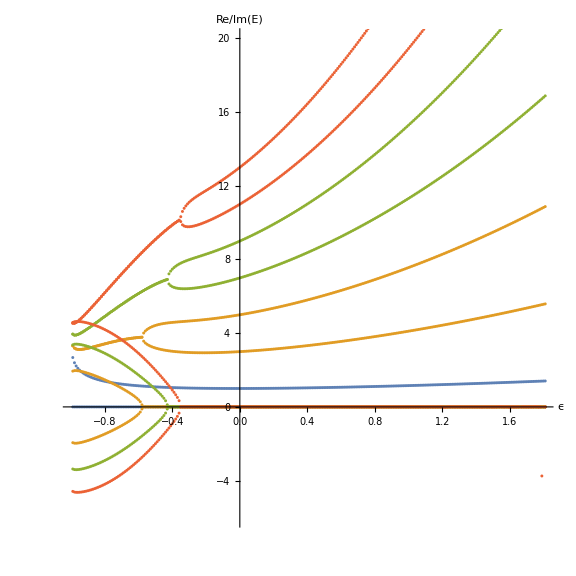

```mathematica
Neig=7;IntRange={-15,15};
epsRange={-0.99,1.8};epsStep=0.01;Neps=(epsRange[[2]]-epsRange[[1]])/epsStep+1;
res=Table[{},{i,Neig}];
Do[eps=epsRange[[1]]+iStep*epsStep;
HAM2=SchrodingerPDEComponent[{FI[x],{x}},<|"ReducedPlanckConstant"->1,"SchrodingerPotential"->x^2(I*x)^eps,"Mass"->1/2|>];
{vals2,funs2}=NDEigensystem[{HAM2,DirichletCondition[FI[x]==0,True]},FI[x],{x,IntRange[[1]],IntRange[[2]]},Neig,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.02}}}}];
Do[AppendTo[res[[i]],{eps,Chop[vals2[[i]],10^-4]}],{i,Neig}]
,{iStep,0,Neps}];
(* Grafica 1*)
ListPlot[res,PlotRange->{epsRange,{0,20}},Joined->True,AspectRatio->1]
(*Traguem parts real i imaginaria*)
dataRe=Table[Map[{#[[1]],Re[#[[2]]]}&,res[[i]]],{i,Neig}];
dataIm=Table[Map[{#[[1]],Im[#[[2]]]}&,res[[i]]],{i,Neig}];
coloresDuo=Table[ColorData[97][1+Ceiling[(i-1)/2]],{i,Neig}];
(* Grafica 2*)
ListPlot[Join[dataRe,dataIm],PlotRange->{epsRange,{-6,20}},Joined->False,AspectRatio->1,PlotStyle->Flatten[{Table[{Thick,coloresDuo[[i]]},{i,Neig}],Table[{Thick,coloresDuo[[i]],Dashed},{i,Neig}] },1],AxesLabel->{Style["ϵ",16],Style["Re/Im(E)",16]},PlotLabel->None,ImageSize->Large]
```